### DSC 101: Wed 25 Sep

#### Commands covered

Below we use mathematical commands not explained in Wolfram, An Elementary Introduction to the Wolfram Language. Descriptions of their usage and examples may be read in the documentation.

##### Important:

```mathematica
MeshFunctions
Mesh
MeshStyle
Function
Flatten
```

##### Secondary:

```mathematica
MeshShading
Large,Medium,Small,Tiny
PointSize,Thickness
Directive
```

Knowing some colors is helpful.

##### Unimportant

All other new functions.

#### Visualizing equation solving

When there are infinitely many solutions, sometimes Solve[] can express the complete solution set in terms of a parameter that looks something like  C[1]. The parameter can take a range of values, which is indicated by C[1]∈ℤ. This is so-called “set notation,” and it indicates that C[1] can be any element of the set ℤ, where ℤ denotes the set of all integers. The symbol ∈ is read, “is an element of”; it is based on the Greek epsilon, but has become somewhat stylized over time.

##### Example

```mathematica
completeSolutionSet=Solve[Sin[x]==1/3,x]
```

{{x→ConditionalExpression[π-ArcSin[1/3]+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[ArcSin[1/3]+2 π C[1], C[1]∈ℤ]}}

What is that C[1]? Syntactically, it is a capital C, and stands for “constant 1”:d

```mathematica
C[1]
```

C[1]

Predict what the following will output:

```mathematica
selectedSolutionSet=Table[completeSolutionSet/.C[1]->c,{c,-2,2}]
selectedSolutionSet=Join@@selectedSolutionSet
```

{{{x→-3 π-ArcSin[1/3]},{x→-4 π+ArcSin[1/3]}},{{x→-π-ArcSin[1/3]},{x→-2 π+ArcSin[1/3]}},{{x→π-ArcSin[1/3]},{x→ArcSin[1/3]}},{{x→3 π-ArcSin[1/3]},{x→2 π+ArcSin[1/3]}},{{x→5 π-ArcSin[1/3]},{x→4 π+ArcSin[1/3]}}}

{{x→-3 π-ArcSin[1/3]},{x→-4 π+ArcSin[1/3]},{x→-π-ArcSin[1/3]},{x→-2 π+ArcSin[1/3]},{x→π-ArcSin[1/3]},{x→ArcSin[1/3]},{x→3 π-ArcSin[1/3]},{x→2 π+ArcSin[1/3]},{x→5 π-ArcSin[1/3]},{x→4 π+ArcSin[1/3]}}

##### First visualization: the familiar NumberLinePlot

A familiar way to visualize the solution set.

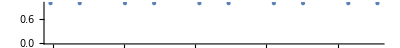

```mathematica
NumberLinePlot[x/.selectedSolutionSet]
```

What does Select[] do in the following?

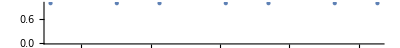

```mathematica
NumberLinePlot[Select[x/.selectedSolutionSet,-10<#<10&]]
```

##### Visualizing with MeshFunctions

Mesh options in plotting functions divide up a plot. Divisions of a curve are indicated by points. A surface divisions are indicated by lines. The divisions are defined by MeshFunctions and Mesh. When the value of a mesh function crosses a mesh value, a plot division is marked. We will focus on meshes on curves.

The Mesh spec is a list of individual mesh specifications, one for each mesh function. For curves there is usually only one mesh function. A mesh specification can be an integer or a list of real numbers. If an integer n, the mesh will be automatically constructed to have n divisions. If a list of values {y_1,y_2,...}, then the mesh will have divisions where the mesh function is equal to each value: f=y_1, f=y_2,...

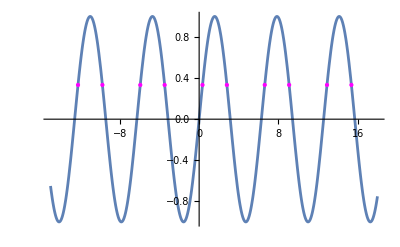

```mathematica
Plot[Sin[x],{x,-15,18},
MeshFunctions->{Function[{x,y},y]},
Mesh->{{1/3}},(* Note: list of lists *)
MeshStyle->Magenta]
```

```mathematica
Plot[Sin[x],{x,-15,18},
MeshFunctions->{Function[{x,y},y]},
Mesh->{{1/3}},
MeshStyle->Directive[PointSize@Medium,Magenta]
]
```

-Graphics-

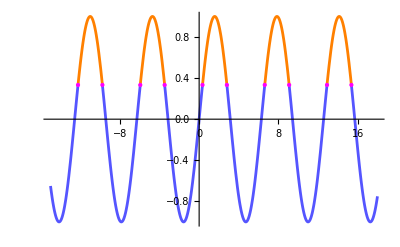

```mathematica
Plot[Sin[x],{x,-15,18},
MeshFunctions->{Function[{x,y},y]},
Mesh->{{1/3}},
MeshStyle->Directive[PointSize@Medium,Magenta],
MeshShading->{Lighter@Blue,Orange}
]
```

```mathematica
Plot[Sin[x],{x,-15,18},
MeshFunctions->{Function[{x,y},y]},
Mesh->{{1/3}},
MeshStyle->Directive[PointSize@Medium,Magenta],
ColorFunction->Function[{x,y},Directive[If[y<1/3,Lighter@Blue,Orange],Opacity[0.4]]],
ColorFunctionScaling->False,
Filling->Automatic
]
```

-Graphics-

Note: Mesh works only on the interior of the plot interval. Solutions at the end points of the domain will not be highlighted. This is because the value of the mesh function has to cross the mesh value. 
	Can you think of another situation where a solution will not be highlighted?

#### Class Activity

We will explore equations of the form f(g(x))=k, where f and g are functions and k is a constant. The goal is to understand how composition affects the solution set.

Explore and compare the following two equations given by the indicated pair of functions:
	sin(ax)=0	sin(x^2)=0	(k=0 in both equations)

```mathematica
f=Function[x,Sin[x]];
g1=Function[{a,x},a*x];
f[g1[a,x]]==0
```

Sin[a x]==0

```mathematica
g2=Function[x,x^2];
f[g2[x]]==0
```

Sin[x^2]==0

The first equation depends on a parameter a.

```mathematica
f[g1[2,x]]==0
```

Sin[2 x]==0

```mathematica
f[g1[3,x]]==0
```

Sin[3 x]==0

Manipulate[] is helpful in visualizing the effect of changing the value of the parameter. We can use it in conjunction with any of the plotting codes above. For instance:

```mathematica
Manipulate[
Plot[f[g1[a,x]],
{x,0,10},(* change domain as desired *)
MeshFunctions->{Function[{x,y},y]},
Mesh->{{0}},(* Note: k goes in the list *)
MeshStyle->Directive[PointSize@Medium,Magenta]],
{{a,1}, (* initial value for a *)
0,10} (* range for a *)
]
```

The second equation does not have a parameter. Manipulate is not particularly useful for it.

##### Questions

How does the density of the solutions change for different ranges of a and x? (In the first equation, for larger a, for an interval for x of a given length, is the number of solutions in the interval roughly the same no matter how large the values of x? For a fixed value of a or in the second equation, is the number of solutions in the interval roughly the same no matter how large the values of x?)

How to explain the differences in the density of solutions in terms of the individuals graphs of f and of g?

In the introductory examples, we had to restrict the domain for visualization. That restricted us to only finitely many solutions. Can we find all solutions?

Assuming that a person could solve the equations f(u)=k and g(x)=c, for any constants k and c, what procedure could they use to solve f(g(x))=k?

#### Mini-project 2

Extend the class activity to other functions for g:
	1. Analyze g(x)=e^x.
	2. Pick your own formula for g(x). Each student should come up with their own formula.

Explain what’s going on in each of the two cases. Refer to the questions above for what to consider. Support your descriptions with appropriate visualizations. The last question is general and should be addressed separately and only once.

Submit a report in the form of a Mathematica note containing text cells, code cells and output, and appropriate visualizations to illustrate the ideas you are conveying.

Note: Be sure that your project reflects creative curiosity. Part of the point of using Mathematica is to push beyond the boundaries of what you can do “by hand.” If you cannot solve the equation but Mathematica can, you should count that as a great success. Also, looking only at an interval like 0<=x<=10 when something really interesting happens when 10<=x<=15 feels like a missed opportunity.

Here’s a cool thing that was only recently added to Mathematica:

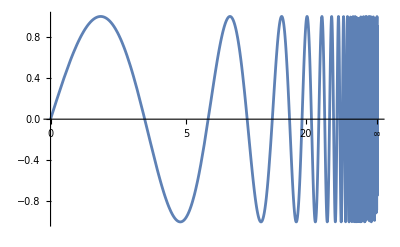

```mathematica
Plot[Sin[x],{x,0,Infinity}]
```